```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[Epi_,T_]:=1/(Exp[Epi/T]-1);
nbd1x[Epi_,T_]:=-1/T nb[Epi,T](nb[Epi,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
(*Epi[q_]:=√(q^2+mp2);*)
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B2thr[Epi_,mf2_,p0_,q_,T_,mu_]:=1/2 (-(1+nb[Epi[q],T])/(2 Epi[q]^3 (-Eq[q,mf2]^2+(-Epi[q]-mu+ⅈ p0)^2))+nbd1x[Epi[q],T]/(2 Epi[q]^2 (-Eq[q,mf2]^2+(-Epi[q]-mu+ⅈ p0)^2))-nb[Epi[q],T]/(2 Epi[q]^3 (-Eq[q,mf2]^2+(Epi[q]-mu+ⅈ p0)^2))+nbd1x[Epi[q],T]/(2 Epi[q]^2 (-Eq[q,mf2]^2+(Epi[q]-mu+ⅈ p0)^2))-nfa[mf2,q,T,mu]/(Eq[q,mf2] (-Epi[q]^2+(-Eq[q,mf2]-mu+ⅈ p0)^2)^2)-(-1+nff[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[q]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)^2)+((1+nb[Epi[q],T]) (-Epi[q]-mu+ⅈ p0))/(Epi[q]^2 (-Eq[q,mf2]^2+(-Epi[q]-mu+ⅈ p0)^2)^2)-(nb[Epi[q],T] (Epi[q]-mu+ⅈ p0))/(Epi[q]^2 (-Eq[q,mf2]^2+(Epi[q]-mu+ⅈ p0)^2)^2));
Zpsi[Epi_,mf2_,h_,p0_,T_,mu_]:=(Nf^2-1)/(2Nf)*h^2/(3 π^2)NIntegrate[q^4 Re[F1B2thr[Epi,mf2,p0,q,T,mu]],{q,1,2000}]+1
```

```mathematica
fpidata=Transpose[Import["../../../sigma0.dat"]];
q=Table[i,{i,1,2000,10}];
T=10;
sigmapi=Flatten[Table[Interpolation[Transpose[{q,√Flatten[Import["../input/T"<>ToString[T]<>"/sigma"<>ToString[i]<>".dat"]]}]],{i,5,400,5}]];
mu=Flatten[Table[i*5.,{i,1,80,1}]];
Length[q];
Length[sigmapidata];
```

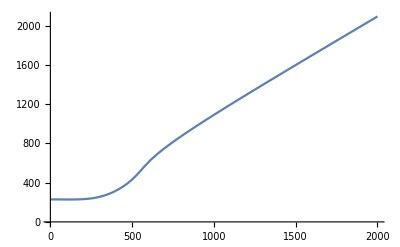

```mathematica
Plot[sigmapi[[61]][q],{q,1,2000}]
```

```mathematica
T=70;
sigmapi=Flatten[Table[Interpolation[Transpose[{q,√Flatten[Import["../input/T"<>ToString[T]<>"/sigma"<>ToString[i]<>".dat"]]}]],{i,5,400,5}]];
data=Table[Zpsi[sigmapi[[i]],mf2[6.5,(fpidata[[T]][[i]])^2/2],6.5,π  T,T,mu[[i]]],{i,1,80}]
Export["./T"<>ToString[T]<>"/Zpsi.dat",data]
```

{1.33219,1.33219,1.3322,1.33222,1.33224,1.33226,1.33229,1.33233,1.33236,1.3324,1.33244,1.33249,1.33253,1.33258,1.33263,1.33268,1.33273,1.33278,1.33283,1.33288,1.33292,1.33296,1.33299,1.33302,1.33304,1.33305,1.33305,1.33304,1.33302,1.33298,1.33293,1.33285,1.33275,1.33263,1.33248,1.33231,1.3321,1.33185,1.33156,1.33122,1.33084,1.3304,1.32989,1.32932,1.32867,1.32792,1.32708,1.32611,1.32498,1.32365,1.32201,1.31989,1.31702,1.31331,1.30911,1.30483,1.30073,1.2969,1.29336,1.29009,1.28707,1.28427,1.28167,1.27925,1.27698,1.27486,1.27287,1.271,1.26922,1.26755,1.26596,1.26445,1.26301,1.26165,1.26034,1.25909,1.25789,1.25675,1.25565,1.25459}

./T70/Zpsi.dat